```mathematica
(* Jackson 3.1 *)
(* ------------- *)
Clear[a,b]
```

```mathematica
Integrate[LegendreP[l,x],{x,0,1}]
```

(√π)/(2 Gamma[1-l/2] Gamma[(3+l)/2])

```mathematica
c[l_]:=Sqrt[Pi]/2/Gamma[1-l/2]/Gamma[(3+l)/2]
```

```mathematica
Table[c[n],{n,0,4}]
```

{1,1/2,0,-1/8,0}

```mathematica
A[l_]:=(2*l+1)/2*c[l]*(a^(l+1)-(-1)^l*b^(l+1))/(a^(2*l+1)-b^(2*l+1))
```

```mathematica
Table[A[n],{n,0,4}]
```

{1/2,(3 (a^2+b^2))/(4 (a^3-b^3)),0,-(7 (a^4+b^4))/(16 (a^7-b^7)),0}

```mathematica
B[l_]:=(2*l+1)/2*c[l]*(a^(l+1)*b^(2*l+1)-(-1)^l*b^(l+1)*a^(2*l+1))/(b^(2*l+1)-a^(2*l+1))
```

```mathematica
Table[B[n],{n,0,4}]
```

{0,(3 (a^3 b^2+a^2 b^3))/(4 (-a^3+b^3)),0,-(7 (a^7 b^4+a^4 b^7))/(16 (-a^7+b^7)),0}

```mathematica
phi4[r_,x_]:=Sum[(A[n]*r^n+B[n]/r^(n+1))*LegendreP[n,x],{n,0,4}]
phi4[r_,x_]:=-0.1 /; r<a
phi4[r_,x_]:=1.1/; r>b
```

```mathematica
phi4[rr,Cos[th]]
```

1/2+((3 (a^3 b^2+a^2 b^3))/(4 (-a^3+b^3) rr^2)+(3 (a^2+b^2) rr)/(4 (a^3-b^3))) Cos[th]+1/2 (-(7 (a^7 b^4+a^4 b^7))/(16 (-a^7+b^7) rr^4)-(7 (a^4+b^4) rr^3)/(16 (a^7-b^7))) (-3 Cos[th]+5 Cos[th]^3)

```mathematica
a=1;b=2;
phi[r_,x_]:=Sum[(A[n]*r^n+B[n]/r^(n+1))*LegendreP[n,x],{n,0,100}]/; (r>1.0 && r<2.0)
phi[r_,x_]:=-0.1 /; (r<1.0 && x<0)
phi[r_,x_]:=-0.1/; (r>2.0 && x>0)
phi[r_,x_]:=1.1 /; (r<1.0 && x>0)
phi[r_,x_]:=1.1/; (r>2.0 && x<0)
```

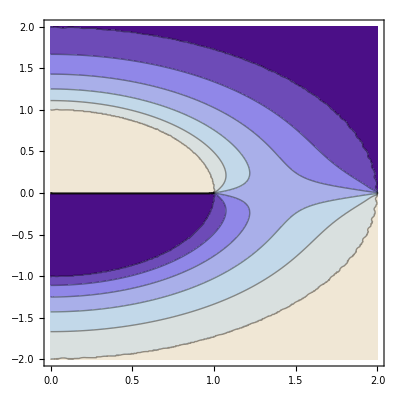

```mathematica
ContourPlot[phi[Sqrt[x^2+y^2],y/Sqrt[x^2+y^2]],{x,0,2},{y,-2,2},PlotPoints->50]
```

```mathematica
(* ContourPlot[phi4[Sqrt[x^2+y^2],y/Sqrt[x^2+y^2]],{x,0,2},{y,-2,2},PlotPoints->50] *)
```

```mathematica
Plot3D[phi[Sqrt[x^2+y^2],y/Sqrt[x^2+y^2]],{x,0,2},{y,-2,2},PlotPoints->50]
```

-Graphics3D-